/home/diogocecilio/projects/dcproj

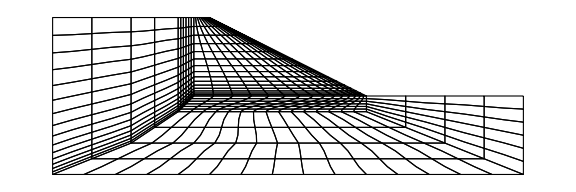

```mathematica
SetDirectory[NotebookDirectory[]]
GenerateGraphics[nodes_,topology_,order_]:=Block[{meshvis,nodevis,v},If[order==1,v={1,2,3,4},v={1,5,2,6,3,7,4,8}];
meshvis=Graphics[{FaceForm[],EdgeForm[Thickness[Tiny]],Opacity[1],GraphicsComplex[nodes,Polygon[topology[[All,v]]]]}];
(*nodevis=Graphics[{MapIndexed[Text[#2[[1]],#1,{-1,1}]&,nodes],{Blue,Point[nodes]}}];*)
nodevis=Graphics[{MapIndexed[Style[Text[#2[[1]],#1,{-1.8,1.8}],FontSize->9]&,nodes],{PointSize[Large],Black,Point[nodes]}}];
{meshvis,nodevis}
];
meshnodes=Import["meshcoords2x1.txt","Table"];
meshnodes=Table[{meshnodes[[i]][[1]],meshnodes[[i]][[2]]},{i,1,Length[meshnodes]}];
meshtopology=Import["meshtopology2x1.txt","Table"];
order=2;
{meshvis,nodevis}=GenerateGraphics[meshnodes,meshtopology+1,order];(*Generates graphics to visualize mesh*)
mesh=Show[meshvis,AspectRatio->Automatic,ImageSize->Large]
boundary=Graphics[{FaceForm[],EdgeForm[Thickness[Tiny]],Opacity[0.1],Polygon[{{0,0},{30,0},{30,5},{20,5},{10,10},{0,10},{0,0}}]}];
```

```mathematica
datainfo[[2,4]]
```

1.15123

```mathematica
datainfo[[100]]
```

```mathematica
id=ToString[100];
ss=StringInsert["information.txt",id,12];
datainfo=Import[ss,"Table"];
```

```mathematica
datainfo
```

{{Monte,Carlo,Sample,=,100},{Safety,Factor,=,1.27451},{r/normr,=,0},{u/normu,=,0},{diff=,100},{diff2,=,100},{counterout,=,10},{CPU,time,=,13.529}}

```mathematica
datasf={};
For[i=1,i≤900,i++,
id=ToString[i];
ss=StringInsert["information.txt",id,12];
datainfo=Import[ss,"Table"];
sf=datainfo[[2,4]];
 If[ToString[sf]=="-nan(ind)"  (*|| datainfo[[6,3]]>0.002*)||datainfo[[3,3]]>0.1 || datainfo[[2,4]]<0.5,
(*If[ datainfo[[2,4]]>0.5 && datainfo[[2,4]]<0.6,
AppendTo[datasf,{i,sf}];
];*)
(*Print[datainfo];*)
(*Continue[];*)
,
(*Print[datainfo];*)
AppendTo[datasf,{i,sf}];
];
];
sortedsf=Sort[ datasf,#1[[2]]<#2[[2]]&];
sortedsf
```

{{766,0.586667},{12,0.586667},{290,0.987013},{773,1.025},{731,1.025},{392,1.025},{145,1.025},{105,1.025},{680,1.07442},{600,1.07442},{205,1.07442},{16,1.07442},{818,1.125},{801,1.125},{581,1.125},{460,1.125},{381,1.125},{368,1.125},{255,1.125},{248,1.125},{184,1.125},{119,1.125},{90,1.125},{870,1.17447},{838,1.17447},{788,1.17447},{762,1.17447},{639,1.17447},{626,1.17447},{623,1.17447},{607,1.17447},{582,1.17447},{552,1.17447},{465,1.17447},{459,1.17447},{395,1.17447},{374,1.17447},{371,1.17447},{363,1.17447},{355,1.17447},{342,1.17447},{319,1.17447},{292,1.17447},{280,1.17447},{204,1.17447},{44,1.17447},{37,1.17447},{898,1.225},{868,1.225},{858,1.225},{853,1.225},{826,1.225},{814,1.225},{811,1.225},{775,1.225},{754,1.225},{732,1.225},{724,1.225},{710,1.225},{691,1.225},{684,1.225},{676,1.225},{664,1.225},{660,1.225},{650,1.225},{644,1.225},{631,1.225},{622,1.225},{616,1.225},{599,1.225},{580,1.225},{551,1.225},{530,1.225},{524,1.225},{516,1.225},{466,1.225},{464,1.225},{444,1.225},{439,1.225},{415,1.225},{376,1.225},{367,1.225},{331,1.225},{318,1.225},{301,1.225},{291,1.225},{229,1.225},{226,1.225},{218,1.225},{217,1.225},{197,1.225},{190,1.225},{121,1.225},{102,1.225},{81,1.225},{75,1.225},{71,1.225},{61,1.225},{35,1.225},{33,1.225},{25,1.225},{11,1.225},{10,1.225},{861,1.27451},{857,1.27451},{819,1.27451},{799,1.27451},{796,1.27451},{786,1.27451},{782,1.27451},{774,1.27451},{772,1.27451},{755,1.27451},{751,1.27451},{746,1.27451},{738,1.27451},{736,1.27451},{728,1.27451},{715,1.27451},{713,1.27451},{698,1.27451},{693,1.27451},{685,1.27451},{679,1.27451},{657,1.27451},{651,1.27451},{638,1.27451},{619,1.27451},{614,1.27451},{608,1.27451},{592,1.27451},{578,1.27451},{563,1.27451},{549,1.27451},{536,1.27451},{535,1.27451},{515,1.27451},{513,1.27451},{511,1.27451},{503,1.27451},{492,1.27451},{473,1.27451},{450,1.27451},{433,1.27451},{417,1.27451},{408,1.27451},{402,1.27451},{356,1.27451},{353,1.27451},{340,1.27451},{329,1.27451},{314,1.27451},{297,1.27451},{286,1.27451},{276,1.27451},{243,1.27451},{219,1.27451},{213,1.27451},{212,1.27451},{196,1.27451},{132,1.27451},{129,1.27451},{122,1.27451},{103,1.27451},{101,1.27451},{100,1.27451},{99,1.27451},{19,1.27451},{9,1.27451},{892,1.325},{889,1.325},{879,1.325},{878,1.325},{877,1.325},{876,1.325},{854,1.325},{835,1.325},{832,1.325},{830,1.325},{827,1.325},{823,1.325},{812,1.325},{802,1.325},{800,1.325},{794,1.325},{749,1.325},{743,1.325},{742,1.325},{739,1.325},{729,1.325},{723,1.325},{720,1.325},{712,1.325},{708,1.325},{682,1.325},{668,1.325},{661,1.325},{656,1.325},{632,1.325},{613,1.325},{601,1.325},{577,1.325},{575,1.325},{557,1.325},{555,1.325},{550,1.325},{547,1.325},{543,1.325},{537,1.325},{534,1.325},{527,1.325},{525,1.325},{518,1.325},{517,1.325},{507,1.325},{504,1.325},{495,1.325},{489,1.325},{484,1.325},{478,1.325},{475,1.325},{453,1.325},{452,1.325},{449,1.325},{442,1.325},{432,1.325},{431,1.325},{425,1.325},{420,1.325},{419,1.325},{406,1.325},{404,1.325},{383,1.325},{330,1.325},{326,1.325},{311,1.325},{300,1.325},{289,1.325},{288,1.325},{279,1.325},{278,1.325},{268,1.325},{263,1.325},{259,1.325},{244,1.325},{233,1.325},{222,1.325},{211,1.325},{207,1.325},{200,1.325},{194,1.325},{187,1.325},{182,1.325},{163,1.325},{159,1.325},{155,1.325},{153,1.325},{141,1.325},{139,1.325},{131,1.325},{125,1.325},{115,1.325},{113,1.325},{110,1.325},{92,1.325},{84,1.325},{83,1.325},{69,1.325},{59,1.325},{47,1.325},{46,1.325},{31,1.325},{27,1.325},{24,1.325},{23,1.325},{22,1.325},{20,1.325},{1,1.325},{891,1.37455},{888,1.37455},{885,1.37455},{881,1.37455},{880,1.37455},{869,1.37455},{866,1.37455},{864,1.37455},{855,1.37455},{847,1.37455},{836,1.37455},{831,1.37455},{817,1.37455},{810,1.37455},{809,1.37455},{803,1.37455},{791,1.37455},{789,1.37455},{783,1.37455},{771,1.37455},{750,1.37455},{737,1.37455},{719,1.37455},{709,1.37455},{706,1.37455},{704,1.37455},{700,1.37455},{695,1.37455},{689,1.37455},{683,1.37455},{671,1.37455},{654,1.37455},{636,1.37455},{625,1.37455},{624,1.37455},{617,1.37455},{605,1.37455},{597,1.37455},{586,1.37455},{584,1.37455},{579,1.37455},{572,1.37455},{567,1.37455},{562,1.37455},{548,1.37455},{544,1.37455},{541,1.37455},{533,1.37455},{519,1.37455},{499,1.37455},{491,1.37455},{488,1.37455},{486,1.37455},{485,1.37455},{480,1.37455},{474,1.37455},{471,1.37455},{469,1.37455},{462,1.37455},{441,1.37455},{435,1.37455},{430,1.37455},{426,1.37455},{418,1.37455},{412,1.37455},{405,1.37455},{400,1.37455},{396,1.37455},{391,1.37455},{384,1.37455},{378,1.37455},{372,1.37455},{370,1.37455},{359,1.37455},{357,1.37455},{351,1.37455},{344,1.37455},{343,1.37455},{337,1.37455},{332,1.37455},{325,1.37455},{312,1.37455},{302,1.37455},{283,1.37455},{269,1.37455},{253,1.37455},{247,1.37455},{237,1.37455},{235,1.37455},{208,1.37455},{206,1.37455},{199,1.37455},{191,1.37455},{188,1.37455},{185,1.37455},{174,1.37455},{173,1.37455},{172,1.37455},{160,1.37455},{154,1.37455},{148,1.37455},{128,1.37455},{118,1.37455},{87,1.37455},{74,1.37455},{70,1.37455},{66,1.37455},{63,1.37455},{62,1.37455},{54,1.37455},{52,1.37455},{43,1.37455},{38,1.37455},{36,1.37455},{34,1.37455},{32,1.37455},{8,1.37455},{899,1.425},{887,1.425},{871,1.425},{867,1.425},{859,1.425},{856,1.425},{851,1.425},{848,1.425},{845,1.425},{844,1.425},{828,1.425},{813,1.425},{804,1.425},{797,1.425},{795,1.425},{793,1.425},{792,1.425},{785,1.425},{767,1.425},{765,1.425},{761,1.425},{740,1.425},{735,1.425},{733,1.425},{730,1.425},{722,1.425},{702,1.425},{692,1.425},{677,1.425},{675,1.425},{672,1.425},{667,1.425},{662,1.425},{655,1.425},{652,1.425},{649,1.425},{645,1.425},{635,1.425},{634,1.425},{630,1.425},{629,1.425},{603,1.425},{598,1.425},{596,1.425},{587,1.425},{583,1.425},{576,1.425},{571,1.425},{568,1.425},{564,1.425},{554,1.425},{539,1.425},{523,1.425},{521,1.425},{506,1.425},{502,1.425},{497,1.425},{496,1.425},{482,1.425},{457,1.425},{438,1.425},{427,1.425},{411,1.425},{403,1.425},{401,1.425},{397,1.425},{385,1.425},{380,1.425},{364,1.425},{348,1.425},{335,1.425},{333,1.425},{324,1.425},{322,1.425},{315,1.425},{307,1.425},{303,1.425},{296,1.425},{293,1.425},{277,1.425},{273,1.425},{266,1.425},{256,1.425},{252,1.425},{251,1.425},{242,1.425},{209,1.425},{193,1.425},{189,1.425},{178,1.425},{177,1.425},{175,1.425},{167,1.425},{164,1.425},{161,1.425},{156,1.425},{152,1.425},{150,1.425},{149,1.425},{147,1.425},{143,1.425},{135,1.425},{127,1.425},{126,1.425},{124,1.425},{114,1.425},{112,1.425},{111,1.425},{106,1.425},{95,1.425},{85,1.425},{76,1.425},{65,1.425},{64,1.425},{57,1.425},{56,1.425},{48,1.425},{41,1.425},{40,1.425},{30,1.425},{29,1.425},{18,1.425},{17,1.425},{7,1.425},{2,1.425},{900,1.47458},{896,1.47458},{895,1.47458},{894,1.47458},{886,1.47458},{884,1.47458},{872,1.47458},{865,1.47458},{860,1.47458},{834,1.47458},{833,1.47458},{829,1.47458},{825,1.47458},{824,1.47458},{821,1.47458},{820,1.47458},{816,1.47458},{798,1.47458},{790,1.47458},{784,1.47458},{753,1.47458},{745,1.47458},{744,1.47458},{734,1.47458},{726,1.47458},{725,1.47458},{718,1.47458},{711,1.47458},{705,1.47458},{697,1.47458},{696,1.47458},{687,1.47458},{678,1.47458},{669,1.47458},{663,1.47458},{659,1.47458},{653,1.47458},{643,1.47458},{642,1.47458},{637,1.47458},{633,1.47458},{627,1.47458},{612,1.47458},{611,1.47458},{609,1.47458},{602,1.47458},{595,1.47458},{593,1.47458},{591,1.47458},{574,1.47458},{573,1.47458},{566,1.47458},{565,1.47458},{556,1.47458},{553,1.47458},{540,1.47458},{529,1.47458},{526,1.47458},{522,1.47458},{520,1.47458},{514,1.47458},{512,1.47458},{508,1.47458},{501,1.47458},{487,1.47458},{479,1.47458},{477,1.47458},{472,1.47458},{470,1.47458},{451,1.47458},{443,1.47458},{440,1.47458},{437,1.47458},{422,1.47458},{407,1.47458},{390,1.47458},{382,1.47458},{365,1.47458},{350,1.47458},{341,1.47458},{334,1.47458},{320,1.47458},{313,1.47458},{310,1.47458},{306,1.47458},{305,1.47458},{295,1.47458},{282,1.47458},{281,1.47458},{270,1.47458},{264,1.47458},{262,1.47458},{261,1.47458},{260,1.47458},{258,1.47458},{257,1.47458},{249,1.47458},{246,1.47458},{230,1.47458},{227,1.47458},{223,1.47458},{220,1.47458},{210,1.47458},{195,1.47458},{183,1.47458},{180,1.47458},{146,1.47458},{123,1.47458},{104,1.47458},{93,1.47458},{91,1.47458},{88,1.47458},{82,1.47458},{72,1.47458},{50,1.47458},{49,1.47458},{42,1.47458},{39,1.47458},{15,1.47458},{14,1.47458},{6,1.47458},{862,1.525},{822,1.525},{815,1.525},{805,1.525},{779,1.525},{777,1.525},{769,1.525},{759,1.525},{756,1.525},{747,1.525},{741,1.525},{717,1.525},{703,1.525},{694,1.525},{674,1.525},{666,1.525},{665,1.525},{647,1.525},{646,1.525},{620,1.525},{618,1.525},{604,1.525},{590,1.525},{589,1.525},{561,1.525},{558,1.525},{545,1.525},{509,1.525},{505,1.525},{498,1.525},{476,1.525},{463,1.525},{448,1.525},{445,1.525},{424,1.525},{421,1.525},{416,1.525},{399,1.525},{379,1.525},{377,1.525},{375,1.525},{347,1.525},{339,1.525},{327,1.525},{323,1.525},{317,1.525},{308,1.525},{287,1.525},{285,1.525},{275,1.525},{267,1.525},{265,1.525},{250,1.525},{241,1.525},{240,1.525},{239,1.525},{238,1.525},{236,1.525},{228,1.525},{225,1.525},{216,1.525},{202,1.525},{198,1.525},{192,1.525},{176,1.525},{170,1.525},{169,1.525},{168,1.525},{162,1.525},{142,1.525},{140,1.525},{134,1.525},{130,1.525},{120,1.525},{117,1.525},{116,1.525},{96,1.525},{79,1.525},{77,1.525},{73,1.525},{68,1.525},{60,1.525},{58,1.525},{55,1.525},{53,1.525},{5,1.525},{897,1.5746},{890,1.5746},{882,1.5746},{852,1.5746},{841,1.5746},{840,1.5746},{839,1.5746},{806,1.5746},{780,1.5746},{778,1.5746},{776,1.5746},{768,1.5746},{760,1.5746},{758,1.5746},{757,1.5746},{752,1.5746},{727,1.5746},{721,1.5746},{699,1.5746},{690,1.5746},{686,1.5746},{681,1.5746},{648,1.5746},{640,1.5746},{628,1.5746},{621,1.5746},{615,1.5746},{594,1.5746},{570,1.5746},{569,1.5746},{546,1.5746},{542,1.5746},{538,1.5746},{493,1.5746},{490,1.5746},{468,1.5746},{455,1.5746},{447,1.5746},{436,1.5746},{434,1.5746},{428,1.5746},{410,1.5746},{398,1.5746},{394,1.5746},{393,1.5746},{388,1.5746},{373,1.5746},{369,1.5746},{362,1.5746},{361,1.5746},{360,1.5746},{358,1.5746},{354,1.5746},{352,1.5746},{336,1.5746},{321,1.5746},{304,1.5746},{299,1.5746},{284,1.5746},{272,1.5746},{254,1.5746},{234,1.5746},{232,1.5746},{214,1.5746},{201,1.5746},{166,1.5746},{157,1.5746},{144,1.5746},{138,1.5746},{137,1.5746},{108,1.5746},{107,1.5746},{98,1.5746},{97,1.5746},{94,1.5746},{80,1.5746},{51,1.5746},{13,1.5746},{4,1.5746},{883,1.625},{875,1.625},{873,1.625},{850,1.625},{842,1.625},{808,1.625},{787,1.625},{763,1.625},{716,1.625},{714,1.625},{673,1.625},{610,1.625},{606,1.625},{585,1.625},{559,1.625},{532,1.625},{528,1.625},{500,1.625},{494,1.625},{481,1.625},{467,1.625},{458,1.625},{389,1.625},{387,1.625},{366,1.625},{349,1.625},{346,1.625},{345,1.625},{316,1.625},{309,1.625},{274,1.625},{245,1.625},{231,1.625},{224,1.625},{221,1.625},{203,1.625},{171,1.625},{136,1.625},{133,1.625},{109,1.625},{89,1.625},{86,1.625},{893,1.67463},{863,1.67463},{764,1.67463},{707,1.67463},{701,1.67463},{688,1.67463},{641,1.67463},{446,1.67463},{423,1.67463},{386,1.67463},{271,1.67463},{181,1.67463},{165,1.67463},{158,1.67463},{45,1.67463},{28,1.67463},{3,1.67463},{849,1.725},{846,1.725},{770,1.725},{588,1.725},{483,1.725},{461,1.725},{429,1.725},{414,1.725},{338,1.725},{78,1.725},{26,1.725},{781,1.77465}}

```mathematica
Export["SFSRM.txt",sortedsf]
```

SFSRM.txt

```mathematica
sortedsf2=sortedsf;
Clear[x]
plots={};
sh={};
curves={};
sum=0;
curvescrit={};
gph=Graphics[{White,Polygon[{{30,10},{50,10},{50,20},{20,20}}]}];
For[ii=1,ii≤30,ii++,
id=ToString[sortedsf2[[ii,1]]];
ss=StringInsert["plasticsqrtj2.txt",id,14];
data=Import[ss,"Table"];
largestdata=Sort[Transpose[ data][[3]],Greater];
newdata={};
coords={};
For[i=1,i<=Length[data],i++,
If[data[[i,3]]>largestdata[[380]],
AppendTo[newdata,{data[[i,1]],data[[i,2]],data[[i,3]]}];
AppendTo[coords,{data[[i,1]],data[[i,2]]}];
];
];


(*Print["id = ",id];*)
model=a x^2 + b x+c;
fit=FindFit[coords,model,{a,b,c},x];
If[fit[[2,2]]>0,
model=a x Exp[-k  x^d ]+b;
fit=FindFit[coords,model,{a,k,b,d},x];
modelf=Function[{x},Evaluate[model/.fit]];
(*Continue[];*)
,
modelf=Function[{x},Evaluate[model/.fit]];
];

(*modelf=NonlinearModelFit[data,model,{a,k,b},x];*)
xrange={10,30};
yrange={5,20};
sum+=modelf[[2]];
If[sortedsf2[[ii,1]]==First[sortedsf][[1]]||sortedsf2[[ii,1]]==Last[sortedsf][[1]],
If[sortedsf2[[ii,1]]==First[sortedsf][[1]],
Print[" Melhor = ",id ];
pl2=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Thick,Green}];
pl=pl2;

AppendTo[curvescrit,pl];
pl=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Black,Thin,Opacity[0.3]}];
,
Print["Pior = ",id ];
pl2=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Thick,Red}];
pl=pl2;

AppendTo[curvescrit,pl];
pl=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Black,Thin,Opacity[0.3]}];
];
,
pl=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Black,Thin,Opacity[0.3]}];
pl2=Plot[modelf[x],{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Black}];
];
plot=ListContourPlot[data,Contours->200,ContourStyle->None,InterpolationOrder->3,PlotRange->{0,Max[Transpose[data][[3]]]},AspectRatio->Automatic,ColorFunction->"TemperatureMap",PerformanceGoal->"Quality",ImageSize->Medium];

sff = ToString[sortedsf2[[ii,2]]];
safetyfactor=StringInsert["Factor of Safety = ",sff,19];
shh=Show[plot,pl,gph,AspectRatio->Automatic,Frame->False,PlotLabel->safetyfactor];
AppendTo[sh,shh];
AppendTo[curves,pl];

];
sum=sum/ii;
```

FindFit::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

Melhor = 766

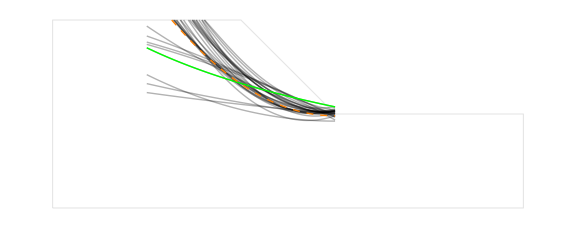

```mathematica
Show[boundary,Show[Table[curves[[i]],{i,1,Length[curves]}],PlotRange->{xrange,yrange}],curvescrit,Plot[sum,{x,xrange[[1]],xrange[[2]]},AspectRatio->Automatic,PlotRange->{xrange,yrange},PlotStyle->{Thick,Orange,Dashed}],AspectRatio->Automatic,ImageSize->Large]
```

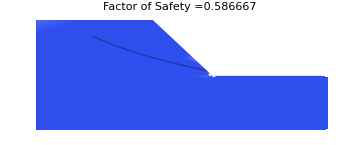
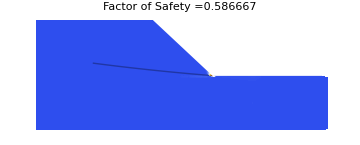
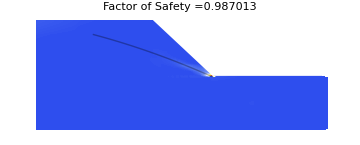
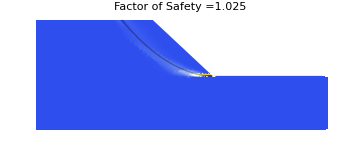
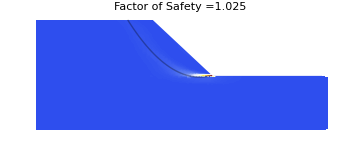
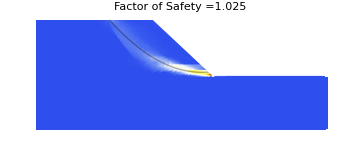
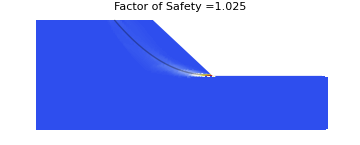
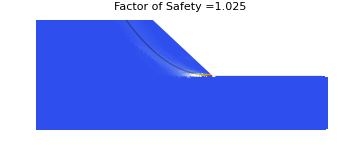
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
sh
```